## Poster pictures

### Introduction

This notebook contains the source code for producing the pictures shown on the poster.

### Warning

All but the first three pictures require a great deal of time or memory (or both).

### Fundamental theorem of algebra

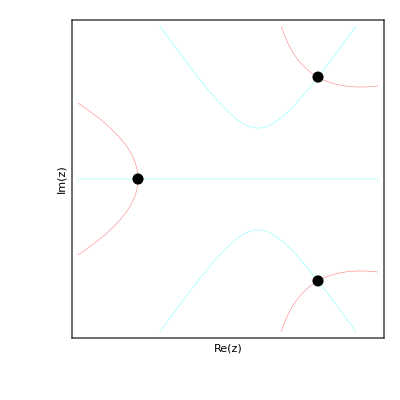

-Graphics3D-

```mathematica
zz=x/.NSolve[ x^3+x+10==0,x];
x1=Floor@Min[Re@zz]-1;
x2=Ceiling@Max[Re@zz]+1;
y1=Floor@Min[Im@zz]-1;
y2=Ceiling@Max[Im@zz]+1;
poly=Expand[Times@@((x+ⅈ y)-#&)/@zz];

Show[{
ContourPlot[Re[poly],{x,x1,x2},{y,y1,y2},Contours->{0},ContourShading->False,ContourStyle->Directive@{RGBColor[1,0,0],Thickness[0.001]},MaxRecursion->4],
ContourPlot[Im[poly],{x,x1,x2},{y,y1,y2},Contours->{0},ContourShading->False,MaxRecursion->4,ContourStyle->Directive@{RGBColor[0,1,1],Thickness[0.001]}],
Graphics[{PointSize[0.02],(Point[{Re[#1],Im[#1]}]&)/@zz}]},FrameTicks->None,FrameLabel->{"Re(z)","Im(z)"}]


Plot3D[Log[Abs[poly]+1],{x,x1,x2},{y,y1,y2},PlotRange->All,Ticks->{None,None,None},PlotTheme->"Web",Axes->{False, False, False},PlotPoints->50]
```

### Icosahedral sphere division

```mathematica
Needs["Graphics`Polyhedra`"]
```

```mathematica
faces=(#1⟦1⟧&)/@PolyhedronData["Dodecahedron"]⟦1⟧;
```

This divides the faces of a dodecahedron into smaller ones:

```mathematica
divide[pentgon_]:=(Append[#1,(Plus@@pentgon)/5]&)/@Flatten[({{#1⟦1⟧,#1⟦3⟧},{#1⟦2⟧,#1⟦3⟧}}&)/@(Append[#1,(Plus@@#1)/2]&)/@Partition[Append[pentgon,First[pentgon]],2,1],1]
```

This colors the faces black and white:

```mathematica
Module[{three,still,color},For[three=Flatten[divide/@faces,1];still=DeleteCases[three,three⟦1⟧];white={};black={three⟦1⟧};color="b",still≠{},Null,temp={};i=1;Which[color=="b",While[temp=={},temp=Select[still,Length[black⟦-i⟧∩#1]==2&];i=i+1;];AppendTo[white,temp⟦1⟧];color="w",color=="w",While[temp=={},temp=Select[still,Length[white⟦-i⟧∩#1]==2&];i=i+1;];AppendTo[black,temp⟦1⟧];color="b"];still=DeleteCases[still,temp⟦1⟧]]]
```

Here is the icosahedral sphere division:

```mathematica
OnSphere[l_List,n_]:=(#1/(√(#1.#1))&)/@Flatten[(Table[Evaluate[First[#1]+(j (Last[#1]-First[#1]))/n],{j,0,n}]&)/@Partition[Append[l,First[l]],2,1],1]
```

```mathematica
Show[Graphics3D[{EdgeForm[],
 {GrayLevel[1], Polygon /@ (OnSphere[#, 3]& /@ white) },
 {GrayLevel[0], Polygon /@ (OnSphere[#, 3]& /@ black) } }],
 Lighting -> False, Boxed -> False, 
 Background -> GrayLevel[0.8]];
```

The next picture shows how the sphere looks after stereographic projection. We drop the faces which have a point which goes to infinity.

```mathematica
StereographicProjection[{x_, y_, z_}]={x/(1+z), y/(1+z)};
```

```mathematica
nwhite = Map[{{0,1,0}, {-1,0,0}, {0,0,1}}.#&,
   Select[white, Plus @@ (Last /@ #)/3 > -0.8505&], {-2}];
nblack=Map[{{0,1,0}, {-1,0,0}, {0,0,1}}.#&,
   Select[black, Plus @@ (Last /@ #)/3 > -0.8505&], {-2}];
Show[Graphics[{
{GrayLevel[0.8], Polygon[Table[
4.5{Cos[i 2Pi/5+Pi/10 //N], Sin[i 2Pi/5+Pi/10//N]}, 
    {i, 0, 4}]]},
{GrayLevel[0], Map[StereographicProjection,
	   Polygon /@ (OnSphere[#,24]& /@ nblack), {-2}]},
{GrayLevel[1], Map[StereographicProjection,
	   Polygon /@ (OnSphere[#,24]& /@ nwhite), {-2}]}}],
    PlotRange->All, AspectRatio->Automatic];
```

### Five octohedra inscribed in an icosahedron

```mathematica
<<Graphics`Polyhedra`
```

```mathematica
mp[i_,j_]:=mp[i,j]=1/2 (Vertices[Icosahedron]⟦i⟧+Vertices[Icosahedron]⟦j⟧)
```

```mathematica
Holed[poly_Polygon,ri_,ra_,opts___]:=Module[{pl,mp,i,o},pl=poly⟦1⟧;mp=(Plus@@pl)/Length[pl];i=(mp+ri (#1-mp)&)/@pl;o=(mp+ra (#1-mp)&)/@pl;i=Reverse/@Partition[Append[i,i⟦1⟧],2,1];o=Partition[Append[o,o⟦1⟧],2,1];{opts,Polygon/@MapThread[Join,{i,o}]}]
```

```mathematica
cross[rn1_,rn2_]:={rn1⟦2⟧ rn2⟦3⟧-rn1⟦3⟧ rn2⟦2⟧,rn1⟦3⟧ rn2⟦1⟧-rn1⟦1⟧ rn2⟦3⟧,rn1⟦1⟧ rn2⟦2⟧-rn1⟦2⟧ rn2⟦1⟧};
```

```mathematica
oct1=Polygon/@{{mp[1,5],mp[6,11],mp[2,3]},{mp[7,12],mp[6,11],mp[2,3]},{mp[1,5],mp[6,11],mp[9,10]},{mp[7,12],mp[6,11],mp[9,10]},{mp[1,5],mp[4,8],mp[2,3]},{mp[7,12],mp[4,8],mp[2,3]},{mp[1,5],mp[4,8],mp[9,10]},{mp[7,12],mp[4,8],mp[9,10]}};
```

```mathematica
Bars[p_,ri_,ra_,rr_]:=Module[{i,o,b,hi,ha},o=(Holed[#1,ri,ra]&)/@p;i=(Holed[#1,ri,ra]&)/@Map[rr #1&,p,{-1}];hi=(Partition[#1,2,1]&)/@(Append[#1,First[#1]]&)/@(#1⟦1⟧&)/@Flatten[i];ha=(Partition[#1,2,1]&)/@(Append[#1,First[#1]]&)/@(#1⟦1⟧&)/@Flatten[o];b=MapThread[Polygon[Join[#1,Reverse[#2]]]&,{hi,ha},2];{o,i,b}]
```

```mathematica
g=Flatten[Bars[oct1,0.9,1,0.95]]//.Polygon[l_]:>Line[Append[l,First[l]]];
```

```mathematica
Do[m[i]=N[{{Cos[(2 π i)/5],Sin[(2 π i)/5],0},{-Sin[(2 π i)/5],Cos[(2 π i)/5],0},{0,0,1}}],{i,0,4}];
```

```mathematica
Show[Graphics3D[{{Thickness[0.006],GrayLevel[0],Dashing[{0.01,0.01}],Polyhedron[Icosahedron]⟦1⟧/.Polygon[l_]:>Line[Append[l,First[l]]]},{Thickness[0.001],Table[{Hue[i/6],Map[m[i].#1&,g,{-2}]},{i,0,4}]}}],Boxed->False];
```

### Riemann surfaces

Using the method of differential reslovents, we can generate the following solutions of the polynomial x^n - x - z for n = 2, 3, 4 and x^5 - x + z.

```mathematica
roots[2,1,z_]=1/2-1/2 HypergeometricPFQ[{-1/2},{},-4 z];
roots[2,2,z_]=1/2+1/2 HypergeometricPFQ[{-1/2},{},-4 z];
roots[3,1,z_]=Hypergeometric2F1[1/6,-1/6,1/2,(27 z^2)/4]+1/2 z Hypergeometric2F1[2/3,1/3,3/2,(27 z^2)/4];
roots[3,2,z_]=-Hypergeometric2F1[1/6,-1/6,1/2,(27 z^2)/4]+1/2 z Hypergeometric2F1[2/3,1/3,3/2,(27 z^2)/4];
roots[3,3,z_]=-(z Hypergeometric2F1[2/3,1/3,3/2,(27 z^2)/4]);
roots[4,1,z_]=-(z HypergeometricPFQ[{1/4,1/2,3/4},{2/3,4/3},-(256 z^3)/27]);
roots[4,2,z_]=HypergeometricPFQ[{-1/12,1/6,5/12},{1/3,2/3},-(256 z^3)/27]+1/3 z HypergeometricPFQ[{1/4,1/2,3/4},{2/3,4/3},-(256 z^3)/27]-2/9 z^2 HypergeometricPFQ[{7/12,5/6,13/12},{4/3,5/3},-(256 z^3)/27];
roots[4,3,z_]=(-1)^(2/3) HypergeometricPFQ[{-1/12,1/6,5/12},{1/3,2/3},-(256 z^3)/27]+1/3 z HypergeometricPFQ[{1/4,1/2,3/4},{2/3,4/3},-(256 z^3)/27]+2/9 (-1)^(1/3) z^2 HypergeometricPFQ[{7/12,5/6,13/12},{4/3,5/3},-(256 z^3)/27];
roots[4,4,z_]=-((-1)^(1/3) HypergeometricPFQ[{-1/12,1/6,5/12},{1/3,2/3},-(256 z^3)/27])+1/3 z HypergeometricPFQ[{1/4,1/2,3/4},{2/3,4/3},-(256 z^3)/27]-2/9 (-1)^(2/3) z^2 HypergeometricPFQ[{7/12,5/6,13/12},{4/3,5/3},-(256 z^3)/27];
roots[5,1,z_]=z HypergeometricPFQ[{1/5,2/5,3/5,4/5},{1/2,3/4,5/4},-(3125 z^4)/256];
roots[5,2,z_]=-(4 (-1)^(1/4) Gamma[3/4] HypergeometricPFQ[{-1/20,3/20,7/20,11/20},{1/4,1/2,3/4},-(3125 z^4)/256])/Gamma[-1/4]-1/4 z HypergeometricPFQ[{1/5,2/5,3/5,4/5},{1/2,3/4,5/4},-(3125 z^4)/256]+(25 (-1)^(3/4) z^2 Gamma[5/4] HypergeometricPFQ[{9/20,13/20,17/20,21/20},{3/4,5/4,3/2},-(3125 z^4)/256])/(128 Gamma[9/4])+1/32 (5 ⅈ) z^3 HypergeometricPFQ[{7/10,9/10,11/10,13/10},{5/4,3/2,7/4},-(3125 z^4)/256];
roots[5,3,z_]=-(4 (-1)^(3/4) Gamma[3/4] HypergeometricPFQ[{-1/20,3/20,7/20,11/20},{1/4,1/2,3/4},-(3125 z^4)/256])/Gamma[-1/4]-1/4 z HypergeometricPFQ[{1/5,2/5,3/5,4/5},{1/2,3/4,5/4},-(3125 z^4)/256]+(25 (-1)^(1/4) z^2 Gamma[5/4] HypergeometricPFQ[{9/20,13/20,17/20,21/20},{3/4,5/4,3/2},-(3125 z^4)/256])/(128 Gamma[9/4])-1/32 (5 ⅈ) z^3 HypergeometricPFQ[{7/10,9/10,11/10,13/10},{5/4,3/2,7/4},-(3125 z^4)/256];
roots[5,4,z_]=(4 (-1)^(1/4) Gamma[3/4] HypergeometricPFQ[{-1/20,3/20,7/20,11/20},{1/4,1/2,3/4},-(3125 z^4)/256])/Gamma[-1/4]-1/4 z HypergeometricPFQ[{1/5,2/5,3/5,4/5},{1/2,3/4,5/4},-(3125 z^4)/256]-(25 (-1)^(3/4) z^2 Gamma[5/4] HypergeometricPFQ[{9/20,13/20,17/20,21/20},{3/4,5/4,3/2},-(3125 z^4)/256])/(128 Gamma[9/4])+1/32 (5 ⅈ) z^3 HypergeometricPFQ[{7/10,9/10,11/10,13/10},{5/4,3/2,7/4},-(3125 z^4)/256];
roots[5,5,z_]=(4 (-1)^(3/4) Gamma[3/4] HypergeometricPFQ[{-1/20,3/20,7/20,11/20},{1/4,1/2,3/4},-(3125 z^4)/256])/Gamma[-1/4]-1/4 z HypergeometricPFQ[{1/5,2/5,3/5,4/5},{1/2,3/4,5/4},-(3125 z^4)/256]-(25 (-1)^(1/4) z^2 Gamma[5/4] HypergeometricPFQ[{9/20,13/20,17/20,21/20},{3/4,5/4,3/2},-(3125 z^4)/256])/(128 Gamma[9/4])-1/32 (5 ⅈ) z^3 HypergeometricPFQ[{7/10,9/10,11/10,13/10},{5/4,3/2,7/4},-(3125 z^4)/256];
```

```mathematica
lists=Table[Graphics3D[Table[({{EdgeForm[],Map[Function[v,Function[m,MapThread[Polygon[Join[#1,Reverse[#2]]]&,(Partition[Append[#1,First[#1]],2,1]&)/@{(m+0.8 (#1-m)&)/@v,v}]][(Plus@@v)/4]],#1,{2}]},{Thickness[0.001],Map[Function[v,Function[m,(Line[Append[#1,First[#1]]]&)[(m+0.8 (#1-m)&)/@v]][(Plus@@v)/4]],#1,{2}]}}&)[Function[p,Flatten[(MapThread[{Join[#1,Reverse[#2]]}&,#1,1]&)/@Partition[(Partition[#1,2,1]&)/@p,2,1],2]]/@Function[{e,b,c},Table[({Re[#1],Im[#1],Re[roots[i,j,#1]]}&)[N[Exp[ⅈ π p] r]],{k,0,2 i-3},{p,(k-c)/c+e,(k-c+1)/c-e,(1/c-2 e)/(12/c)},{r,e,b,(b-e)/6}]][1/10.^12,(2. (#1^#1/i^i)^(1/#1)&)[i-1],i-1]],{j,i}],PlotRange->All,Boxed->False,BoxRatios->{1,1,2},ViewPoint->{1,-1.3,1.3},PlotLabel->{"Quadratic","Cubic","Quartic","Quintic"}⟦i+1⟧],{i,2,5}]
```

Part::partw: {Quadratic,Cubic,Quartic,Quintic} 的部分 5 不存在.

Part::partw: {Quadratic,Cubic,Quartic,Quintic} 的部分 6 不存在.

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Riemann surface of Quintic

```mathematica
<<Graphics`Graphics3D`
```

```mathematica
RE[y_]:=Module[{hyps},hyps={-(4 Gamma[3/4] HypergeometricPFQ[{-1/20,3/20,7/20,11/20},{1/4,1/2,3/4},-(3125 y^4)/256])/Gamma[-1/4],y HypergeometricPFQ[{1/5,2/5,3/5,4/5},{1/2,3/4,5/4},-(3125 y^4)/256],(5 y^2 Gamma[5/4] HypergeometricPFQ[{9/20,13/20,17/20,21/20},{3/4,5/4,3/2},-(3125 y^4)/256])/(8 Gamma[9/4]),1/6 y^3 HypergeometricPFQ[{7/10,9/10,11/10,13/10},{5/4,3/2,7/4},-(3125 y^4)/256]};(hyps.#1&)/@{{0,1,0,0},{(-1)^(1/4),-1/4,5/16 ((-1)^(1/4))^3,15/16 ((-1)^(1/4))^2},{(-1)^(3/4),-1/4,5/16 ((-1)^(3/4))^3,15/16 ((-1)^(3/4))^2},{-(-1)^(1/4),-1/4,5/16 (-(-1)^(1/4))^3,15/16 (-(-1)^(1/4))^2},{-(-1)^(3/4),-1/4,5/16 (-(-1)^(3/4))^3,15/16 (-(-1)^(3/4))^2}}]
```

```mathematica
nr = 20; np = 7; Table[tab[j] =
Table[{r Cos[p],r Sin[p],#}& /@ 
     RE[ Chop[N[ r Exp[I p] ] ] ],
   {r,10.^-4,N[2 (4^4/5^5)^(1/4)],
        N[(2 (4^4/5^5)^(1/4) -10^-4) /nr] },
   {p,j Pi/4+10.^-4,j Pi/4 + Pi/4-10.^-4,
        (Pi/4-2 10.^-4)/np} ] // N, {j,0,7} ] ;
```

```mathematica
Do[mt[i,j+1] = Map[#[[i]]&,tab[j] // N,{2}],{i,5},{j,0,7}]
```

```mathematica
Do[b[i,j] = ListSurfacePlot3D[  
     Map[MapAt[Abs,#,3]&,mt[i,j],{2}],Axes->True,
DisplayFunction->Identity],{i,5},{j,8}]
```

```mathematica
BB=Graphics3D[ Show[ Flatten[Table[b[i,j],{i,5},{j,8}]] ,
     Axes->True] ];
```

```mathematica
Show[Graphics3D[{
{EdgeForm[],SurfaceColor[GrayLevel[1/2],
     RGBColor[1/2,1/2,1]],
Function[poly,Module[{mp,p1,p2,p3,p4,
pn1,pn2,pn3,pn4,fac=0.8},mp=Plus @@ poly[[1]]/4;
{p1,p2,p3,p4}=poly[[1]];pn1=mp+fac(p1-mp);
pn2=mp+fac(p2-mp);pn3=mp+fac(p3-mp);
pn4=mp+fac(p4-mp);{Polygon[{p1,p2,pn2,pn1}],
Polygon[{p2,p3,pn3,pn2}],Polygon[{p3,p4,pn4,pn3}],
Polygon[{p4,p1,pn1,pn4}]}] ] /@ Flatten[ BB[[1,1]] ] },
{Thickness[0.001],GrayLevel[0],
Function[poly,Module[{mp,p1,p2,p3,p4,
pn1,pn2,pn3,pn4,fac=0.8},mp=Plus @@ poly[[1]]/4;
{p1,p2,p3,p4}=poly[[1]];pn1=mp+fac(p1-mp);
pn2=mp+fac(p2-mp);pn3=mp+fac(p3-mp);
pn4=mp+fac(p4-mp); 
Line[{pn1,pn2,pn3,pn4,pn1}]]] /@ 
     Flatten[ BB[[1,1]] ]} } ],
PlotRange->All,Axes->False,Boxed->False, LightSources -> 
{{{1.,0.,1.},RGBColor[1,0,0]},{{1.,1.,1.},
     RGBColor[0,1,0]}, 
 {{1.,-1.,-1.},RGBColor[0,1,0]},{{0.,1.,-1.},
     RGBColor[0,0,1]},
 {{0.,1.,1.},RGBColor[0,0,1]},{{-1.,-1.,-1.},
    RGBColor[0,1,0]}},
BoxRatios->{1,1,3/2},ViewPoint->{1,-1.3,1.3}];
```